Inicialmente se iban a considerar más ejemplos, pero se ha hecho muy largo y los casos ‘generales’ no se han estudiando, aunque sí hemos generado datos.

## Definimos la función.

```mathematica
c=3*10^5; (*km/s*)
Ωk[Ωm_,ΩΛ_,Ωr_]=1-Ωr-Ωm-ΩΛ;
Eint[z_,Ωm_,ΩΛ_,Ωr_]:=Sqrt[Ωr*(1+z)^4+Ωm*(1+z)^3+Ωk[Ωm,ΩΛ,Ωr]*(1+z)^2+ΩΛ];
integral[z_,Ωm_,ΩΛ_,Ωr_]:=NIntegrate[1/Eint[zint, Ωm,ΩΛ,Ωr], {zint, 0, z}];
dL[z_,H0_,Ωm_,ΩΛ_,Ωr_]:=Which[
Ωk[Ωm,ΩΛ,Ωr]>0,
(
(c*(1+z))/(Sqrt[Abs[Ωk[Ωm,ΩΛ,Ωr]]]*H0)*Sinh[Sqrt[Abs[Ωk[Ωm,ΩΛ,Ωr]]]*integral[z,Ωm,ΩΛ,Ωr]]
),
Ωk[Ωm,ΩΛ,Ωr]<0,
(
(c*(1+z))/(Sqrt[Abs[Ωk[Ωm,ΩΛ,Ωr]]]*H0)*Sin[Sqrt[Abs[Ωk[Ωm,ΩΛ,Ωr]]]*integral[z,Ωm,ΩΛ,Ωr]]
),
Ωk[Ωm,ΩΛ,Ωr]==0,
(
(c*(1+z))/H0*integral[z,Ωm,ΩΛ,Ωr]
)
]
modDistancia[z_,H0_,Ωm_,ΩΛ_,Ωr_]:=-5+5*Log10[dL[z,H0,Ωm,ΩΛ,Ωr]*10^6]
```

```mathematica
dL[11,30,0.1,0.6,0]
```

465785.

```mathematica
modDistancia[1,70,0.3,0.7,0]
```

44.1017

## Parámetros de la ejecución

```mathematica
numPuntos=500;
maxZ=1000;
zDivision=5; (* Como el ascenso del inicio es tan abrupto, aumentamos la densidad de puntos en esa zona *)
```

## Generamos datos para un modelo abierto (Ωk < 0) y H0 fijo

```mathematica
(*vectorZ1 =RandomReal[{0, zDivision}, Round[numPuntos/3]];
vectorZ2 = RandomReal[{zDivision, maxZ}, Round[2*numPuntos/3]];*)
```

```mathematica
(*vectorZ = Join[vectorZ1, vectorZ2];*)
```

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
```

```mathematica
Ωm=0.7; ΩΛ=0.8; Ωr=0;H0=70;
```

```mathematica
{tiempo,resultadosAbierto}=AbsoluteTiming[Map[modDistancia[#,H0,Ωm,ΩΛ,Ωr]&,vectorZ]];
```

```mathematica
guardar=Transpose[{vectorZ, resultadosAbierto}];
nombresVariables={"vectorZ", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/H0="<>ToString[H0]<>"_Om="<>ToString[Ωm]<>"_Ol="<>ToString[ΩΛ]<>"_Or="<>ToString[Ωr]<>"_Ok="<>ToString[ Ωk[Ωm, ΩΛ,Ωr]]<>".csv";
```

```mathematica
Export[ruta,guardar,"CSV"];
```

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Ωk = ", Ωk[Ωm, ΩΛ,Ωr]]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Ωk = -0.5

Número de datos: 1000

Tiempo de ejecución en segundos: 3.23168

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/H0=70_Om=0.7_Ol=0.8_Or=0_Ok=-0.5.csv

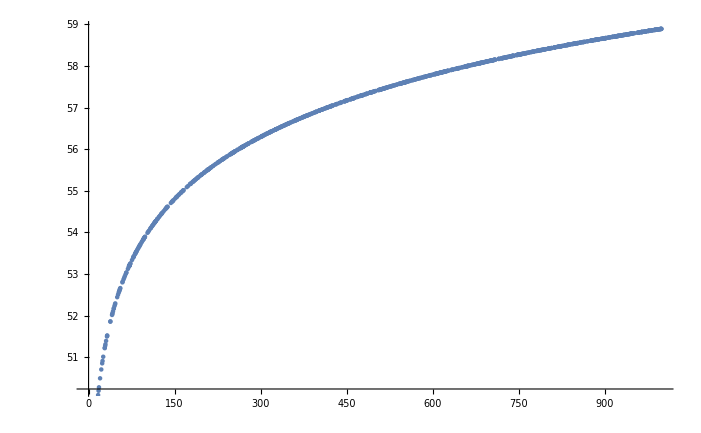

```mathematica
ListPlot[Transpose[{vectorZ,resultadosAbierto}]]
```

```mathematica
Take[vectorZ, 10]
```

{740.489,463.998,893.292,557.284,415.236,618.565,51.3508,54.3859,574.398,976.244}

```mathematica
Take[resultadosAbierto, 10]
```

{58.2433,57.2346,58.6485,57.6298,56.9952,57.8549,52.5058,52.6287,57.6951,58.8404}

## Generamos datos para un modelo cerrado (Ωk > 0)

```mathematica
vectorZ1 =RandomReal[{0, zDivision}, Round[numPuntos/2]];
vectorZ2 = RandomReal[{zDivision, maxZ}, Round[numPuntos/2]];
vectorZ = Join[vectorZ1, vectorZ2];
```

```mathematica
(*vectorZ=RandomReal[{0, maxZ}, numPuntos];*)
```

```mathematica
AppendTo[vectorZ, 0.1];
AppendTo[vectorZ, maxZ];
```

```mathematica
Ωm=0.3; ΩΛ=0.3; Ωr=0;H0 =40;
```

```mathematica
{tiempo,resultadosCerrado}=AbsoluteTiming[Map[modDistancia[#,H0,Ωm, ΩΛ, Ωr]&,vectorZ]];
```

```mathematica
guardar=Transpose[{vectorZ, resultadosCerrado}];
nombresVariables={"vectorZ", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/H0="<>ToString[H0]<>"_Om="<>ToString[Ωm]<>"_Ol="<>ToString[ΩΛ]<>"_Or="<>ToString[Ωr]<>"_Ok="<>ToString[ Ωk[Ωm, ΩΛ,Ωr]]<>"_numPuntos_"<>ToString[numPuntos]<>".csv";
```

```mathematica
Export[ruta,guardar,"CSV"];
```

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Ωk = ", Ωk[Ωm, ΩΛ,Ωr]]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Ωk = 0.4

Número de datos: 502

Tiempo de ejecución en segundos: 1.31621

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/H0=40_Om=0.3_Ol=0.3_Or=0_Ok=0.4_numPuntos_500.csv

## Generamos datos para un modelo plano (Ωk = 0)

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
```

```mathematica
Ωm=0.3; ΩΛ=0.7; Ωr=0;H0=90;
```

```mathematica
{tiempo,resultadosPlano}=AbsoluteTiming[Map[modDistancia[#,H0,Ωm,ΩΛ,Ωr]&,vectorZ]];
```

```mathematica
guardar=Transpose[{vectorZ, resultadosPlano}];
nombresVariables={"vectorZ", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/H0="<>ToString[H0]<>"_Om="<>ToString[Ωm]<>"_Ol="<>ToString[ΩΛ]<>"_Or="<>ToString[Ωr]<>"_Ok="<>ToString[ Ωk[Ωm, ΩΛ,Ωr]]<>".csv";
```

```mathematica
Export[ruta,guardar,"CSV"];
```

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Ωk = ", Ωk[Ωm, ΩΛ,Ωr]]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Ωk = 0.

Número de datos: 1000

Tiempo de ejecución en segundos: 2.66648

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/H0=90_Om=0.3_Ol=0.7_Or=0_Ok=0..csv

## Generemos modelos abiertos (Ωk < 0) con distintos valores de las Ω y H0

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
vectorOm = RandomReal[{0, 1}, numPuntos];
vectorOl ={} ;
Do[
elemento=vectorOm[[i]];
numAleatorio=RandomReal[{0, 1-elemento-0.001}];
AppendTo[vectorOl, numAleatorio];
,{i, Length[vectorOm]}
]
vectorH0 = RandomReal[{50, 100}, numPuntos];
```

```mathematica
Take[vectorOm, 10]
```

{0.136917,0.980453,0.12888,0.114705,0.969373,0.427476,0.416498,0.6039,0.258833,0.0833772}

```mathematica
Take[vectorOl, 10]
```

{0.811811,0.00686588,0.248995,0.141167,0.01806,0.262863,0.371728,0.207519,0.568393,0.1786}

```mathematica
{tiempo,resultadosAbierto2}=AbsoluteTiming[MapThread[modDistancia,{vectorZ,vectorH0,vectorOm,vectorOl,ConstantArray[0,Length@vectorZ]}]];
```

```mathematica
guardar=Transpose[{vectorZ, vectorH0, vectorOm, vectorOl,  resultadosAbierto2}];
nombresVariables={"vectorZ", "vectorH0", "vectorOm", "vectorOl", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/valores_libres_abierto.csv";
```

```mathematica
Export[ruta,guardar,"CSV"]
```

/home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_abierto.csv

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Modelo abierto (Ωk < 0)"]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Modelo abierto (Ωk < 0)

Número de datos: 1000

Tiempo de ejecución en segundos: 2.80187

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_abierto.csv

## Generemos modelos cerrados (Ωk > 0) con distintos valores de las Ω y H0

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
vectorOm = RandomReal[{0, 1}, numPuntos];
vectorOl ={} ;
Do[
elemento=vectorOm[[i]];
numAleatorio=RandomReal[{1-elemento+0.001, 1}];
AppendTo[vectorOl, numAleatorio];
,{i, Length[vectorOm]}
]
vectorH0 = RandomReal[{50, 100}, numPuntos];
```

```mathematica
Take[vectorOm, 10]
```

{0.0049557,0.737422,0.433468,0.307216,0.705913,0.191761,0.349329,0.857981,0.887141,0.77004}

```mathematica
Take[vectorOl, 10]
```

{0.996382,0.516001,0.815832,0.877752,0.472041,0.963178,0.693255,0.760309,0.337521,0.730983}

```mathematica
{tiempo,resultadosCerrado2}=AbsoluteTiming[MapThread[modDistancia,{vectorZ,vectorH0,vectorOm,vectorOl,ConstantArray[0,Length@vectorZ]}]];
```

```mathematica
guardar=Transpose[{vectorZ, vectorH0, vectorOm, vectorOl,  resultadosCerrado2}];
nombresVariables={"vectorZ", "vectorH0", "vectorOm", "vectorOl", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/valores_libres_cerrado.csv";
```

```mathematica
Export[ruta,guardar,"CSV"]
```

/home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_cerrado.csv

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Modelo abierto (Ωk < 0)"]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Modelo abierto (Ωk < 0)

Número de datos: 1000

Tiempo de ejecución en segundos: 2.98306

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_cerrado.csv

## Generemos modelos planos (Ωk=0) con distintos valores de las Ω y H0

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
vectorOm = Round[RandomReal[{0, 1}, numPuntos], 0.001];
vectorOl =1-vectorOm;
vectorH0 = RandomReal[{50, 100}, numPuntos];
```

```mathematica
Take[vectorOm, 10]
```

{0.943,0.999,0.139,0.124,0.56,0.16,0.455,0.131,0.382,0.034}

```mathematica
Take[vectorOl, 10]
```

{0.057,0.001,0.861,0.876,0.44,0.84,0.545,0.869,0.618,0.966}

```mathematica
{tiempo,resultadosPlano2}=AbsoluteTiming[MapThread[modDistancia,{vectorZ,vectorH0,vectorOm,vectorOl,ConstantArray[0,Length@vectorZ]}]];
```

```mathematica
guardar=Transpose[{vectorZ, vectorH0, vectorOm, vectorOl, resultadosPlano2}];
nombresVariables={"vectorZ", "vectorH0", "vectorOm", "vectorOl", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/valores_libres_plano.csv";
```

```mathematica
Export[ruta,guardar,"CSV"]
```

/home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_plano.csv

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Modelo abierto (Ωk < 0)"]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Modelo abierto (Ωk < 0)

Número de datos: 1000

Tiempo de ejecución en segundos: 2.80691

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_plano.csv

## Generemos modelos aleatorios con distintos valores de las Ω y H0

```mathematica
vectorZ=RandomReal[{0, maxZ}, numPuntos];
vectorOm =RandomReal[{0, 1}, numPuntos];
vectorOl =RandomReal[{0, 1}, numPuntos];
vectorH0 = RandomReal[{50, 100}, numPuntos];
```

```mathematica
Take[vectorOm, 10]
```

{0.263828,0.667128,0.192158,0.181967,0.134086,0.590336,0.174676,0.495125,0.860563,0.60121}

```mathematica
Take[vectorOl, 10]
```

{0.212435,0.625893,0.831472,0.836722,0.795905,0.0107845,0.377951,0.288505,0.82769,0.730484}

```mathematica
{tiempo,resultadosAleatorio}=AbsoluteTiming[MapThread[modDistancia,{vectorZ,vectorH0,vectorOm,vectorOl,ConstantArray[0,Length@vectorZ]}]];
```

```mathematica
guardar=Transpose[{vectorZ, vectorH0, vectorOm, vectorOl, resultadosAleatorio}];
nombresVariables={"vectorZ", "vectorH0", "vectorOm", "vectorOl", "resultados"};
guardar=Prepend[guardar,nombresVariables];
```

```mathematica
ruta=NotebookDirectory[]<>"Data/valores_libres_aleatorio.csv";
```

```mathematica
Export[ruta,guardar,"CSV"]
```

/home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_aleatorio.csv

```mathematica
s=OpenAppend[ruta];
Do[WriteString[s,ToString[Length[vectorZ]]<> ","<>ToString[tiempo]]];
Close[s];
```

```mathematica
Print["Modelo abierto (Ωk < 0)"]
Print["Número de datos: ", Length[vectorZ]]
Print["Tiempo de ejecución en segundos: ", tiempo]
Print["Ruta del archivo: ", ruta]
```

Modelo abierto (Ωk < 0)

Número de datos: 1000

Tiempo de ejecución en segundos: 3.07074

Ruta del archivo: /home/jaime/Documents/IA/Trabajo Final/Data/valores_libres_aleatorio.csv